## Modelo SEIR para evaluar vacunación e intervenciones no farmaceuticas . Versión “Run”

```mathematica
SetDirectory["D:\\Oscar Mendoza\\Documents\\UINIVERSIDAD\\MAESTRIA\\UNIVERSIDAD DE ANTIOQUIA\\II\\Proyecto\\Documento\\FINAL"]
```

D:\Oscar Mendoza\Documents\UINIVERSIDAD\MAESTRIA\UNIVERSIDAD DE ANTIOQUIA\II\Proyecto\Documento\FINAL

```mathematica
Clear[Na,Nv,Nm,EstX,EstXI,EstXA];
Na=16(*Número de grupos etáreos*);
Nv=2(*Número de dosis de vacunación: 0 dosis, 1 dosis, 2 dosis*);
Nm=3(*Número de grupos de latencia*);
EstX={F,SI,SA,Q}(*Estados de la infección para los expuestos, variable de estado Ex*);
EstXI={F,SI,SA,QF,QS} (*Estados de la infección para los infectados sintomáticos, variable de estado In*);
EstXA={F,S,Q}(*Estados de la infección para los infectados asintomáticos, variable de estado A*);
```

```mathematica
Clear[VarS,VarE,VarI,VarA,VarAll];
VarS=Table[Subscript[S,a,v][t],{a,1,Na},{v,0,Nv}]//Flatten;
VarE=Table[Subscript[Ex,EstX[[x]],m,a,v][t],{x,1,4},{m,1,Nm},{a,1,Na},{v,0,Nv}]//Flatten;
VarI=Table[Subscript[In,EstXI[[x]],a,v][t],{x,1,5},{a,1,Na},{v,0,Nv}]//Flatten;
VarA=Table[Subscript[A,EstXA[[x]],a,v][t],{x,1,3},{a,1,Na},{v,0,Nv}]//Flatten;
VarAll={VarS,VarE,VarI,VarA}//Flatten;
```

```mathematica
numVar=Length/@{VarS,VarE,VarI,VarA,VarAll}
numVarTotal=Total[%//Most]
```

{48,576,240,144,1008}

1008

### Parámetros Base

V1[t,a] tasa de vacunación de la 1ra dosis por grupo de edad "a".
V2[t,a] tasa de vacunación de la 2 dosis por grupo de edad "a".

Npol es el vector de los grupos de edad. Son 16 grupos etáreos. Datos tomados del DANE 2019. N_a población total para el de grupo edad “a”.

ϵ  es la tasa de progresión de la enfermedad (1/ϵ es la duración de la clase de latencia). intϵ es el intervalo de confianza. Aparece en las ecuaciones de los expuestos, infecciosos y asintomáticos. Puede usarse en la calibración del modelo (por ejemplo a datos de muertes). El periodo de latencia (el tiempo en pasar del estado Expuesto a Infeccioso o Asintomático, en términos de la media de una distribución de Erlang) es M*(1/ϵ). M (Nm en la simulación) = 3 es el número de clases de latencia.

d_a es la probabilidad de mostrar síntomas en el grupo de edad "a".

H es la proporción de casos en cuarentena de los infecciosos sintomáticos. Es un parámetro clave para los diferentes escenarios. Puede tomar un valor constante o cambiar en el tiempo. Aparece en las ecuaciones de Inf (Infecciosos).

γ es  la tasa de recuperación (tasa de salida del estado del estado infeccioso sintomático In y asintomático A ). 1/γ es el tiempo de salida. intγ es el intervalo de confianza para γ. Aparece en las ecuaciones de Inf (Infecciosos) y A (Asintomáticos). Podría ser un parámetro de ajuste. Se usa el valor del artículo. También se puede usar para un análisis de sensibilidad.

βnV[t] es el cambio en la transmisibilidad del virus done un valor de 1 es la transmisibilidad de la cepa original. Sirve como parámetro de modelación (escenario) o puede ajustarse de análisis de datos.

ϕ o ϕR es un parámetro entre 0 y 1 que  escala (modula) las medidas de confinamiento (NPI) multiplicando las matrices de contacto por ϕ o (1-ϕ). ϕ = 0 son los valores normales (es decir movilidad y contactos típicos) y ϕ = 1 son los valores de confinamiento estricto. Aparece en las matrices de contacto que están en la fuerzas de infección. Lo vamos a considerar variable de escenario.  Como esta variable depende del tiempo (de la historia natural de la pandemia y sirve para los escenarios de NPI, la haré depender del tiempo),

{qh, qw, qs, qo}. Son los parámetros que me definen los valores umbrales de las matrices de contacto para confinamiento estricto. Se definen como {qh = 1.25, qw = 0.2, qs = 0 y qo = 0.05} lo que significa que para confinamiento extremo los contactos en el hogar aumentan 125%, los contactos en el trabajo disminuyen 80%, los contactos en la escuela disminuyen 100% y en otros se disminuye 95%.

vecd es el vector de probabilidad de mostrar síntomas severos dependiente de la edad.

τ Nivel de transmisión relativo de un asintomático A comparado con el sintómatico I.
intτ es el intervalo de confianza de τ. Usaremos los valores del artículo.

vecσ vector de susceptibilidades dependientes de la edad.

σ_a susceptibilidad (a la transmisión, es decir que tan rápido los susceptibles S pasan a los expuestos E) dependiente de la edad. En la fig S13 se denomina Eficacia a la infección.

σ_av susceptibilidad dependiente de la edad y la dosis de vacunación (es una reducción en la susceptibilidad por la vacunación).

{p1, p2} es la protección contra la infección para 1 o 2 dosis respecto a no vacunar: p1 = 1-(σ_a1/σ_a0) y  p2 = 1-(σ_a2/σ_a0)

f={f0,f1, f2} es la eficacia contra la enfermedad severa para 0, 1 o 2 dosis. Involucra los factores {z1, z2}: f1 = 1-z1 y f2 = 1-z2

```mathematica
Clear[param,vecd,vecσ,f,σ,H,ϕ,βnV,Npol,V,distage];
param={ϵ=0.08,intϵ={0.02,0.08},γ=0.03,intγ={0.37,1.0},τ=0.25,intτ={0.10,0.41}};
vecd={0.07,0.02,0.03,0.04,0.07,0.1, 0.11,0.09,0.1,0.13,0.19,0.27,0.29,0.54,0.63,0.8};
Table[Subscript[d, a]=vecd[[a]],{a,1,16}];
vecσ={0.7,0.42,0.5,0.55,0.7,0.8,0.8,0.8,0.8,0.8,0.9,1.0,1.1,1.3,1.4,1.5};
{p1=0.48,p2=0.6};
f={0,0.7,0.88};
σ[a_,v_]:=vecσ[[a]]*If[v==0,1,If[v==1,(1-p1),(1-p2)]];
H=0.40;

ϕ[t_]=If[t<=28,0.1,If[t<=187,0.63,0.4]](*Escenario base*)

{qh=1.25,qw=0.2,qs=0,qo=0.05};
βnV[t]:= 0.05;(*Bajaremos la transmisión*)
Npol={4658707,3899198,3992100,4190096,4281144,4040414,3702664,3455164,3034042,2867983,2773879,2442560,1959073,1483840,1060819,1553995};
Np=Total[Npol];
distage=Npol/Np;
Table[Subscript[N, a]=Npol[[a]],{a,1,16}];

(*Tasa de vacunación hasta septiembre 2021*)

V1[t_,a_]:=V1[t,a]=If[t<=31,59985,If[t<=61,52005,If[t<=92,111808,If[t<=122,147632,If[t<=153,182928,If[t<=184,157006,90616]]]]]]*distage[[a]]/Npol[[a]];

V2[t_,a_]:=V2[t,a]=If[t<=31,9419,If[t<=61,39724,If[t<=92,51739,If[t<=122,112116,If[t<=153,93022,If[t<=184,75760,57001]]]]]]*distage[[a]]/Npol[[a]];
```

### Condiciones Iniciales

Voy a definir CIs para el inicio de la epidemia. El caso índice en Colombia es una mujer de 19 años en Bogotá.

Se cambian las CIs para la fecha de inicio de vacunación (1 de marzo 2021). Se tienen 141124 casos activos que se asumiran “In”. De aquí tenemos 94083 “A”

```mathematica
Clear[IniS,IniEx,IniIn,IniA,IniAll,Ncasos,Ndh];
Ncasos=141124; (*Numero de casos activos al 1 de marzo*)
Ndh= 60611; (*Numero de fallecidos al 1 de marzo*)
IniIn={Table[Subscript[In,EstXI[[x]],a,0][0]==Ncasos*distage[[a]]/5,{x,1,5},{a,1,Na}],Table[Subscript[In,EstXI[[x]],a,v][0]==0,{x,1,5},{a,1,Na},{v,1,Nv}]}//Flatten;
IniA={Table[Subscript[A,EstXA[[x]],a,0][0]==2*Ncasos*distage[[a]]/9,{x,1,3},{a,1,Na}],Table[Subscript[A,EstXA[[x]],a,v][0]==0,{x,1,3},{a,1,Na},{v,1,Nv}]}//Flatten;
IniEx={Table[Subscript[Ex,EstX[[x]],m,a,0][0]==4Ncasos*distage[[a]]/12,{x,1,4},{m,1,Nm},{a,1,Na}],Table[Subscript[Ex,EstX[[x]],m,a,v][0]==0,{x,1,4},{m,1,Nm},{a,1,Na},{v,1,Nv}]}//Flatten;
IniS={Table[Subscript[S,a,0][0]==Subscript[N, a]-Ncasos*distage[[a]]*17/3-Ndh*distage[[a]],{a,1,Na}],Table[Subscript[S,a,v][0]==0,{a,1,Na},{v,1,Nv}]}//Flatten;
IniAll={IniS,IniEx,IniIn,IniA}//Flatten;
Length[IniAll]
```

1008

```mathematica
(*IniS={Table[Subscript[S,a,0][0]==Subscript[N, a],{a,1,Na}],Table[Subscript[S,a,v][0]==0,{a,1,Na},{v,1,Nv}]}//Flatten;
IniEx=Table[Subscript[Ex,EstX[[x]],m,a,v][0]==0,{x,1,4},{m,1,Nm},{a,1,Na},{v,0,Nv}]//Flatten;
IniIn={Table[Subscript[In,EstXI[[x]],a,0][0]==KroneckerDelta[a,4]KroneckerDelta[x,1],{x,1,5},{a,1,Na}],Table[Subscript[In,EstXI[[x]],a,v][0]==0,{x,1,5},{a,1,Na},{v,1,Nv}]}//Flatten;
IniA={Table[Subscript[A,EstXA[[x]],a,0][0]==0,{x,1,3},{a,1,Na}],Table[Subscript[A,EstXA[[x]],a,v][0]==0,{x,1,3},{a,1,Na},{v,1,Nv}]}//Flatten;
IniAll={IniS,IniEx,IniIn,IniA}//Flatten;
Length[IniAll]*)
```

```mathematica
Clear[βold,βH,βW,βS,βO,βN];
βold=Import["D:\\Oscar Mendoza\\Documents\\UINIVERSIDAD\\MAESTRIA\\UNIVERSIDAD DE ANTIOQUIA\\II\\Proyecto\\Documento\\FINAL\\Bases de datos\\MatricesCol.xlsx","Data"];
βH=(1-(1-qh)ϕ[t])βold[[2]];
βW=(1-(1-qw)ϕ[t])βold[[5]];
βS=(1-(1-qs)ϕ[t])βold[[4]];
βO=(1-(1-qo)ϕ[t])βold[[3]];
βN=(βS+βW+βO);
```

```mathematica
(*Clear[Subscript[λ,F][a,v,t]];*)
Subscript[λ,F][a_,v_,t_]:=βnV[t]*σ[a,v]*Sum[(Subscript[In,F,b,u][t]+Subscript[In,SI,b,u][t]+Subscript[In,SA,b,u][t]+τ(Subscript[A,F,b,u][t]+Subscript[A,S,b,u][t]))*βN[[b,a]],{b,1,Na},{u,0,Nv}];
Subscript[λ,SI][a_,v_,t_]:=βnV[t]*σ[a,v]*Sum[Subscript[In,F,b,u][t]*βH[[b,a]],{b,1,Na},{u,0,Nv}];
Subscript[λ,SA][a_,v_,t_]:=βnV[t]*σ[a,v]*τ*Sum[Subscript[A,F,b,u][t]*βH[[b,a]],{b,1,Na},{u,0,Nv}];
Subscript[λ,Q][a_,v_,t_]:=βnV[t]*σ[a,v]*Sum[Subscript[In,QF,b,u][t]*βH[[b,a]],{b,1,Na},{u,0,Nv}];
```

```mathematica
Clear[EcuS,EcuS1, EcuS2,EcuE1,EcuE2, EcuIn1, EcuIn2,EcuIn3,EcuIn4, EcuIn5, EcuA1,EcuA2,EcuA3,EcuAll] ;
```

```mathematica
EcuS=
Table[D[Subscript[S,a,0][t],t]==-(Sum[Subscript[λ,EstX[[x]]][a,0,t],{x,1,4}]*Subscript[S, a,0][t]/Subscript[N, a])-V1[t,a]Subscript[S, a,0][t],{a,1,Na}];
EcuS1=
Table[D[Subscript[S,a,1][t],t]== 
V1[t,a]Subscript[S, a,0][t]-(Sum[Subscript[λ,EstX[[x]]][a,1,t],{x,1,4}]*Subscript[S, a,1][t]/Subscript[N, a])-V2[t,a]Subscript[S, a,1][t],{a,1,Na}]; 
EcuS2 =
Table[D[Subscript[S,a,2][t],t] == 
V2[t,a]Subscript[S, a,1][t]-(Sum[Subscript[λ,EstX[[x]]][a,2,t],{x,1,4} ])*Subscript[S, a,2][t]/Subscript[N, a],{a,1,Na}];
```

```mathematica
EcuE1=Table[D[Subscript[Ex,EstX[[x]],1,a,v][t],t]==Subscript[λ,EstX[[x]]][a,v,t]*Subscript[S, a,v][t]/Subscript[N, a]-Nm*ϵ*Subscript[Ex,EstX[[x]],1,a,v][t],{x,1,4},{a,1,Na},{v,0,Nv}]//Flatten;
EcuE2=Table[D[Subscript[Ex,EstX[[x]],m,a,v][t],t]==Nm*ϵ*Subscript[Ex,EstX[[x]],m-1,a,v][t]-Nm*ϵ*Subscript[Ex,EstX[[x]],m,a,v][t],{x,1,4},{m,2,Nm},{a,1,Na},{v,0,Nv}]//Flatten;
```

```mathematica
EcuIn1=Table[D[Subscript[In, F,a,v][t], t]==Subscript[d, a] (1-H) Nm ϵ Subscript[Ex, F,Nm,a,v][t]-γ Subscript[In, F,a,v][t],{a,1,Na},{v,0,Nv}];
EcuIn2=Table[D[Subscript[In, SI,a,v][t], t]==Subscript[d, a] Nm ϵ Subscript[Ex, SI,Nm,a,v][t]-γ Subscript[In, SI,a,v][t],{a,1,Na},{v,0,Nv}];
EcuIn3=Table[D[Subscript[In, SA,a,v][t], t]==Subscript[d, a] (1-H) Nm ϵ Subscript[Ex, SA,Nm,a,v][t]-γ Subscript[In, SA,a,v][t],{a,1,Na},{v,0,Nv}];
EcuIn4 = Table[D[Subscript[In,QF,a,v][t],t]==
Subscript[d, a]*H* Nm* ϵ *(Subscript[Ex,F, Nm,a,v][t])-γ* Subscript[In, QF,a,v][t],{a,1,Na}, {v,0,Nv}];
EcuIn5 = Table[D[Subscript[In,QS,a,v][t],t]== Subscript[d, a]*H* Nm* ϵ *(Subscript[Ex,SA, Nm,a,v][t])+ Subscript[d, a]*Nm*ϵ * (Subscript[Ex,Q,Nm,a,v][t])-γ*Subscript[In,QS,a,v][t],{a,1,Na}, {v,0,Nv}];
```

```mathematica
EcuA1 = Table[D[Subscript[A,F,a,v][t],t]== (1-Subscript[d, a])*Nm*ϵ* Subscript[Ex,F,Nm,a,v][t]-γ*Subscript[A,F,a,v][t],{a,1,Na}, {v,0,Nv}]//Flatten;
EcuA2 = Table[D[Subscript[A,S,a,v][t],t]== (1-Subscript[d, a])*Nm *ϵ*((Subscript[Ex, SI, Nm, a, v][t])+ Subscript[Ex, SA, Nm, a, v][t])-γ*Subscript[A, S, a,v][t],{a,1,Na}, {v,0,Nv}]//Flatten;
EcuA3 = Table[D[Subscript[A,Q,a,v][t],t] == (1-Subscript[d, a])*Nm*ϵ*Subscript[Ex,Q,Nm,a,v][t]-γ*Subscript[A,Q,a,v][t],{a,1,Na}, {v,0,Nv}]//Flatten;
```

```mathematica
EcuAll={EcuS,EcuS1,EcuS2,EcuE1,EcuE2, EcuIn1, EcuIn2,EcuIn3,EcuIn4, EcuIn5, EcuA1,EcuA2,EcuA3}//Flatten;
Length[EcuAll]
```

1008

## Solución del Modelo

```mathematica
Clear[sol];
sol=NDSolve[{EcuAll,IniAll}//Flatten,VarAll,{t,0,240}];
```

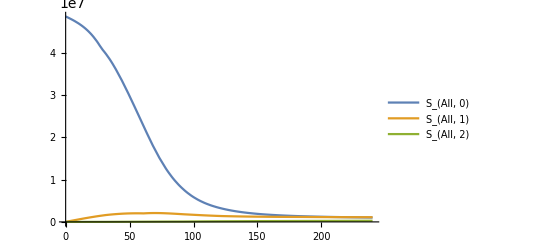

```mathematica
Plot[{Evaluate[Sum[Subscript[S, a,0][t],{a,1,16}]/.sol],Evaluate[Sum[Subscript[S, a,1][t],{a,1,16}]/.sol],Evaluate[Sum[Subscript[S, a,2][t],{a,1,16}]/.sol]},{t,0,240},PlotRange->All,PlotLegends->{"S_(All, 0)","S_(All, 1)","S_(All, 2)"}]
```

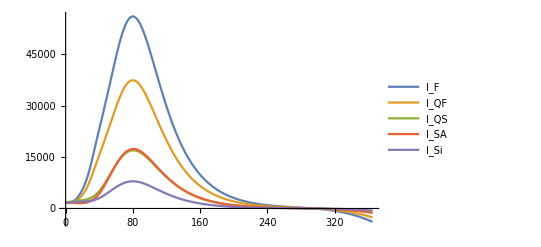

```mathematica
Plot[Evaluate[{Subscript[In, F,10,0][t],Subscript[In, QF,10,0][t],Subscript[In, QS,10,0][t],Subscript[In, SA,10,0][t],Subscript[In, SI,10,0][t]}/.sol],{t,0,365},PlotRange->All,PlotLegends->{"I_F","I_QF","I_QS","I_SA","I_Si"}]
```

## Salidas del modelo (Cantidades medibles de salud pública)

Se importa la lista con el número de días transcurrido entre la fecha de inicio de síntomas y el fallecimiento . Con esta lista constuyo la distribución de probabilidad de retrazo Lag[R] que me da la probabilidad de fallecer  dado un retrazo de R días . Los datos del INS muestran un número importante de personas que tienen retrazo 0, es decir la fecha de inicio de síntomas y la fecha de fallecimiento es la misma. Eliminamos estos datos anómalos que sesgan la distribución. PIs2D es la probabilidad de fallecer por grupo etáreo dado que presentó síntomas, datos para Colombia INS .

```mathematica
Clear[dF2D,dF2DNew,dEmp,Lag,PIs2D]
dF2D=
Import["D:\\Oscar Mendoza\\Documents\\UINIVERSIDAD\\MAESTRIA\\UNIVERSIDAD DE ANTIOQUIA\\II\\Proyecto\\Documento\\FINAL\\Bases de datos\\daysFisToDeath.csv"]//Flatten;
dF2DNew=Cases[dF2D,Except[0]];
Lag=EmpiricalDistribution[dF2DNew];
dEmp=Import["D:\\Oscar Mendoza\\Documents\\UINIVERSIDAD\\MAESTRIA\\UNIVERSIDAD DE ANTIOQUIA\\II\\Proyecto\\Documento\\FINAL\\Bases de datos\\Casos_COVID\\Casos_COVID\\fallecidos_pos_mar2.csv"]//Rest;
PIs2D={74,16,5*3,20*3,193,385,196*3,1000,535*3,2143,1064*3,1600*3,6283,7162,7337,18976}/53829;
```

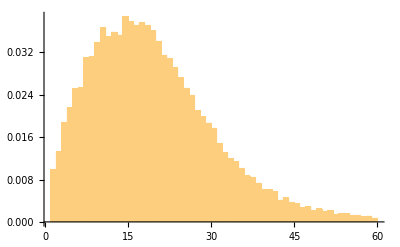

```mathematica
Histogram[dF2DNew,{1,60,1},"PDF"]
```

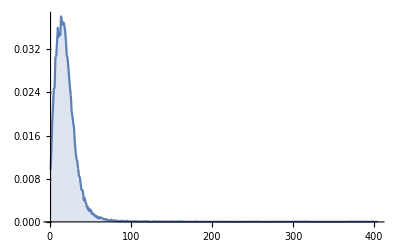

```mathematica
DiscretePlot[PDF[Lag,x],{x,dF2DNew}]
```

Inf[a,v,t] es el número de infecciosos sintomáticos para el grupo de edad "a" y de vacunación "v" en el día "t". Debo sumar sobre todas las clases de Infecciosos sintomáticos (F, QF, QS, SA, SI).
NewInf[a,v,t] el número de nuevos infecciosos sintomáticos en el día "t" para el grupo "a" y "v". El número de nuevos infecciosos puede ser cero si la población en el día "t" es menor que en el día "t-1".
ND[d] es el número de muertes en el día "d".

```mathematica
Clear[Inf2,NewInf, ND];
Inf2[a_,v_,tt_]:=Inf2[a,v,tt]=Part[Evaluate[Subscript[In, F,a,v][t]+Subscript[In, QF,a,v][t]+Subscript[In, QS,a,v][t]+Subscript[In, SA,a,v][t]+Subscript[In, SI,a,v][t]/.sol]/.t->tt,1];
NewInf[a_,v_,t_]:=NewInf[a,v,t]=If[Inf2[a,v,t]>Inf2[a,v,t-1],Inf2[a,v,t]-Inf2[a,v,t-1],0];
ND[d_]:=ND[d]=Sum[PIs2D[[a]]*PDF[Lag,R]*NewInf[a,v,d-R]*(1-f[[v+1]]),{a,1,16},{v,0,2},{R,1,d-1}]
```

```mathematica
Table[{t,Sall=Evaluate[Sum[Subscript[S, a,0][t],{a,1,16}]/.sol],Eall=Evaluate[Sum[Subscript[Ex, EstX[[x]],m,a,0][t],{a,1,16},{m,1,Nm},{x,1,4}]/.sol],Iall=Evaluate[Sum[Subscript[In, EstXI[[x]],a,0][t],{a,1,16},{x,1,5}]/.sol],Aall=Evaluate[Sum[Subscript[A, EstXA[[x]],a,0][t],{a,1,16},{x,1,3}]/.sol],Sall+Eall+Iall+Aall},{t,0,240,15}]//TableForm
```

0 | 4.85354×10^7 | 564496. | 141124. | 94082.7 | 4.93351×10^7
15 | 3.51015×10^7 | 693030. | 165722. | 551797. | 3.6512×10^7
30 | 2.49585×10^7 | 893091. | 187754. | 1.00492×10^6 | 2.70442×10^7
45 | 1.76653×10^7 | 757569. | 208068. | 1.36281×10^6 | 1.99937×10^7
60 | 1.23496×10^7 | 671305. | 210870. | 1.50377×10^6 | 1.47355×10^7
75 | 8.55574×10^6 | 550351. | 202682. | 1.5095×10^6 | 1.08183×10^7
90 | 5.88711×10^6 | 423909. | 184724. | 1.40678×10^6 | 7.90252×10^6
105 | 4.03453×10^6 | 309885. | 160396. | 1.23462×10^6 | 5.73944×10^6
120 | 2.76161×10^6 | 216936. | 133453. | 1.03124×10^6 | 4.14323×10^6
135 | 1.89275×10^6 | 146741. | 107016. | 826766. | 2.97327×10^6
150 | 1.30147×10^6 | 96689.8 | 83169.8 | 640769. | 2.1221×10^6
165 | 899033. | 62487. | 62959. | 482973. | 1.50745×10^6
180 | 624412. | 39824.6 | 46625. | 355807. | 1.06667×10^6
195 | 432706. | 28522.2 | 33948.9 | 257591. | 752768.
210 | 299303. | 20126.3 | 24740.2 | 186571. | 530740.
225 | 207661. | 13397.1 | 17948.4 | 134449. | 373455.
240 | 144564. | 8815.62 | 12908.2 | 95991.7 | 262280.

```mathematica
DthEmp=Take[dEmp[[;;,2]],239];
```

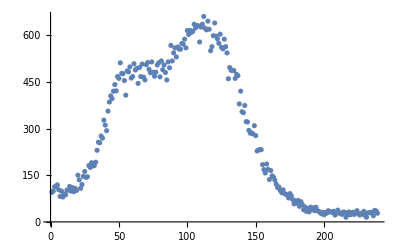

```mathematica
g1=ListPlot[DthEmp]
```

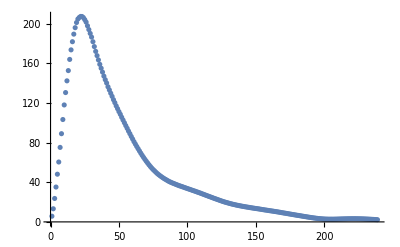

ListPlot

```mathematica
lDvo=Table[ND[d],{d,2,240}];
g2=ListPlot[lDvo]

ListPlot
```

```mathematica
TB0=Total[lD21]
```

60982.6